```mathematica
NS["evidences_2neurons"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\neurobayes\\"
```

C:\Users\pglpm\repositories\neurobayes\

```mathematica
xlogy[x_,y_]:=If[x>0,x*Log[x/y],0];entr[p1_,p2_]:=Total[MapThread[xlogy,{p1,p2}]];
entr2[p1_,p2_]:=Total[MapThread[xlogy,{p2,p1}]];
```

```mathematica
values=Flatten@Import["states2n_values.csv"];
pos=Flatten@Import["states2n_pos.csv"];
posi[i_]:=Pick[pos,values,i];
n=Max[pos]
```

417461

```mathematica
nstates=Range[0,3];states=SparseArray[pos->values];
```

```mathematica
frequencies[ss_,0]=0;frequencies[ss_,nn_]:=Pick[Join[#[[2]],{0,0,0,0}],Join[#[[1]],Range[0,3]],ss][[1]]&@T@Tally[states[[;;nn]]];
SetAttributes[frequencies,Listable];
occur[i_]:=SparseArray[{states[[i]]+1->1},{4}];
```

```mathematica
prob[ss_,nn_,la_,ff_]:=(la*ff+frequencies[ss,nn])/(la+nn);
SetAttributes[prob,Listable];
tprob[nn_,la_,ff_]:=prob[nstates,nn,la,ff];
surprise[i_,la_,ff_]:=-Log[prob[states[[i]],i-1,la,ff]//N];
SetAttributes[surprise,Listable];
```

```mathematica
finfreqs=frequencies[nstates,n]/n;finfreqs//N
```

{0.973871,0.00555022,0.0204594,0.000119772}

```mathematica
prob[3,0,10^-12,1/4]//N
```

0.25

```mathematica
rg=Union@Complement[Round@Range[1,n,n/200],posi[1],posi[2],posi[3]];Length@rg
```

192

```mathematica
pc=4;fc=1/4;rg=Union@Complement[Round@Range[1,n,n/200],posi[1],posi[2],posi[3]];
l1=Length@posi[1];l2=Length@posi[2];l3=Length@posi[3];

((Mean@surprise[posi[1][[1;;;;Round[l1/100]]],pc,fc]//N)*l1+(Mean@surprise[posi[2][[1;;;;Round[l2/100]]],pc,fc]//N)*l2+(Mean@surprise[posi[3],pc,fc]//N)*l3+(Mean@surprise[rg,pc,fc]//N)*(n-l1-l2-l3))/n
```

0.134676

```mathematica
pc=10^-12;fc=1/4;rg=Union@Complement[Round@Range[1,n,n/200],posi[1],posi[2],posi[3]];
l1=Length@posi[1];l2=Length@posi[2];l3=Length@posi[3];

((Mean@surprise[posi[1][[1;;;;Round[l1/100]]],pc,fc]//N)*l1+(Mean@surprise[posi[2][[1;;;;Round[l2/100]]],pc,fc]//N)*l2+(Mean@surprise[posi[3],pc,fc]//N)*l3+(Mean@surprise[rg,pc,fc]//N)*(n-l1-l2-l3))/n
```

0.136329

```mathematica
pc=4;fc=1/4;rg=Complement[RandomInteger[{1,n},500],posi[1],posi[2],posi[3]];
l1=Length@posi[1];l2=Length@posi[2];l3=Length@posi[3];

((Mean@surprise[RandomSample[posi[1],100],pc,fc]//N)*l1+(Mean@surprise[RandomSample[posi[2],100],pc,fc]//N)*l2+(Mean@surprise[posi[3],pc,fc]//N)*l3+(Mean@surprise[rg,pc,fc]//N)*(n-l1-l2-l3))/n
```

0.135505

```mathematica
pc=10^-12;fc=1/4;rg=Complement[RandomInteger[{1,n},500],posi[1],posi[2],posi[3]];
l1=Length@posi[1];l2=Length@posi[2];l3=Length@posi[3];

((Mean@surprise[RandomSample[posi[1],100],pc,fc]//N)*l1+(Mean@surprise[RandomSample[posi[2],100],pc,fc]//N)*l2+(Mean@surprise[posi[3],pc,fc]//N)*l3+(Mean@surprise[rg,pc,fc]//N)*(n-l1-l2-l3))/n
```

0.135535

```mathematica
points=Sort@Union[Flatten@{Table[posi[i][[1;;;;Ceiling[Length[posi[i]]/100]]],{i,3}],Round@Range[1,n,n/100]}];Length[points]
```

346

```mathematica
points[[1;;50]]
```

{1,81,2236,2455,2518,3630,4176,5973,7112,8350,8534,11842,11917,12525,12851,12865,13494,16290,16699,17247,18660,20874,22005,22331,22688,25049,27146,29223,29835,30829,31026,31032,33038,33398,33897,36855,37572,39871,41747,43916,44071,45872,45922,46724,47784,49037,50096,50688,51161,53355}

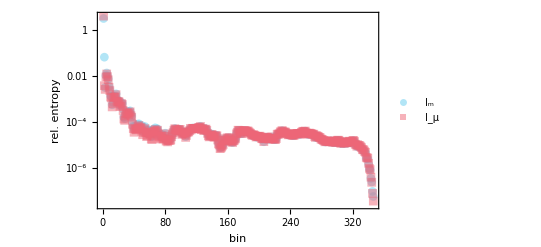

```mathematica
fixLogPlots@ListLogPlot[T@Table[{entr[tprob[i,4,Table[1/4,{4}]],finfreqs],entr[tprob[i,10^-12,Table[1/4,{4}]],finfreqs]},{i,points}],PlotStyle->{Opacity[0.5],Opacity[0.5]},Axes->None,Frame->{{True,False},{True,False}},FrameLabel->{{"rel. entropy",None},{bin,None}},PlotMarkers->Auto,PlotLegends->mylegends[{Subscript[Style[Ι,Italic],"m"],Subscript[Style[Ι,Italic],Style[μ,FontSlant->Plain]]},{Scaled[{0,0}],{0,0}}],Joined->False,PlotRange->Auto]
```

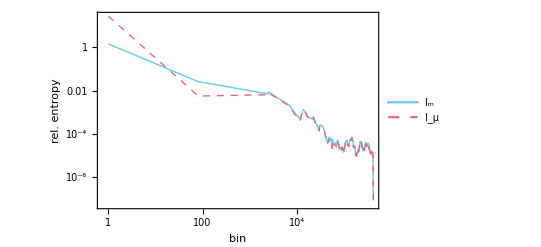

```mathematica
fixLogPlots@ListLogLogPlot[{Table[{i,entr2[tprob[i,4,Table[1/4,{4}]],finfreqs]},{i,points}],Table[{i,entr2[tprob[i,10^-12,Table[1/4,{4}]],finfreqs]},{i,points}]},PlotStyle->{Thick,Dashed,DotDashed},Axes->None,Frame->{{True,False},{True,False}},FrameLabel->{{"rel. entropy",None},{bin,None}},PlotLegends->mylegendsv[{Subscript[Style[Ι,Italic],"m"],Subscript[Style[Ι,Italic],Style[μ,FontSlant->Plain]]},labelposition[{1,1}]],Joined->True,PlotRange->Auto]
```

```mathematica
expdf0["comp_priors"]
```

comp_priors.pdf

```mathematica
fixLogPlots@ListLogPlot[{Table[{i,entr2[tprob[i,4,Table[1/4,{4}]],occur[i]]},{i,points}],Table[{i,entr2[tprob[i,10^-12,Table[1/4,{4}]],occur[i]]},{i,points}]},PlotStyle->Auto,Axes->None,Frame->{{True,False},{True,False}},FrameLabel->{{"surprises",None},{bin,None}},PlotMarkers->Auto,PlotLegends->mylegendsv[{Subscript[Style[Ι,Italic],"m"],Subscript[Style[Ι,Italic],Style[μ,FontSlant->Plain]]},labelposition[{1,1}]],Joined->False,PlotRange->{10^-2,All}]
```

$Aborted

```mathematica
expdf0["surprises2"]
```

surprises2.pdf

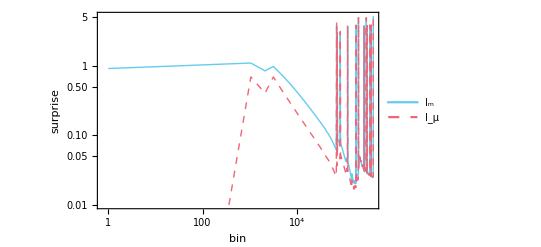

```mathematica
rg=n;points=Union@Round[10^Range[0,Log[10,rg],Log[10,rg]/500]];fixLogPlots@ListLogLogPlot[T@Table[{entr2[tprob[i,4,Table[1/4,{4}]],occur[i]],entr2[tprob[i,10^-12,Table[1/4,{4}]],occur[i]]},{i,points}],DataRange->{1,rg},PlotStyle->{Thick,Dashed,DotDashed},Axes->None,Frame->{{True,False},{True,False}},FrameLabel->{{"surprise",None},{bin,None}},PlotLegends->mylegends[{Subscript[Style[Ι,Italic],"m"],Subscript[Style[Ι,Italic],Style[μ,FontSlant->Plain]]},labelposition[{0,0}]],Joined->True,PlotRange->{10^-2,All}]
```

```mathematica
expdf0["surprise2"]
```

surprise2.pdf

```mathematica
Length[pos]
```

10908

```mathematica
posi[i_]:=Pick[pos,values,i];
```

```mathematica
points=Sort@Union[Flatten@{Table[posi[i][[1;;;;Round[Length[posi[i]]/50]]],{i,3}],Round@Range[1,n,n/50]}];Length[points]
```

200

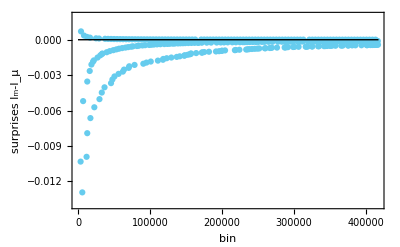

```mathematica
ListPlot[Table[{i,entr2[tprob[i,4,Table[1/4,{4}]],occur[i]]-entr2[tprob[i,10^-12,Table[1/4,{4}]],occur[i]]},{i,points}],PlotStyle->Auto,Axes->None,Frame->{{True,False},{True,False}},FrameLabel->{{surprises Subscript[Style["Ι",Italic],"m"] - Subscript[Style["Ι",Italic],Style["μ",FontSlant->Plain]],None},{bin,None}},PlotStyle->Black,PlotLegends->None(*mylegends[{Subscript[Style[Ι,Italic],"m"],Subscript[Style[Ι,Italic],Style[μ,FontSlant->Plain]]},labelposition[{0,0}]]*),Joined->False,PlotRange->{-0.014,0.002},Epilog->{Line[{{1,0},{n,0}}]},ImageSize->a5rsize]
```

```mathematica
expdf0["diff_surprises"]
```

diff_surprises.pdf

```mathematica
expng["diff_surprises",%%]
```

diff_surprises.png

```mathematica
surprise[
```

```mathematica
states[[300]]
```

0

```mathematica
xlogy[2,0]
```

∞

```mathematica
SparseArray[{states[[300]]+1->1}]
```

SparseArray[…]

```mathematica
occur[i_]:=SparseArray[{states[[i]]+1->1},{4}];
```

```mathematica
occur[500]//MF
```

(1
0
0
0)

```mathematica
t={0,0,0,0};t[[2]]=1;t
```

{0,1,0,0}

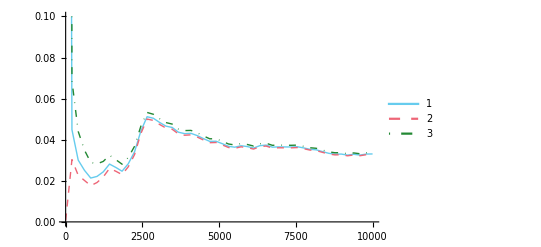

```mathematica
rg=10000;points=Round@Range[1,rg,rg/50];ListPlot[T@Table[{entr2[tprob[i,4,Table[1/4,{4}]],occur[i]],entr2[tprob[i,0.001,Table[1/4,{4}]],occur[i]],entr2[tprob[i,40,{75,10,10,5}/100],occur[i]]},{i,points}],DataRange->{1,rg},PlotStyle->{Thick,Dashed,DotDashed},PlotLegends->Auto,Joined->True,PlotRange->{0,0.1}]
```

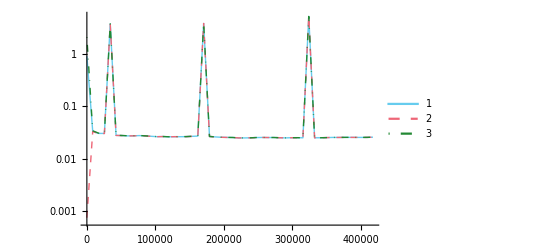

```mathematica
rg=n;points=Round@Range[1,rg,rg/50];ListLogPlot[T@Table[{entr2[tprob[i,4,Table[1/4,{4}]],occur[i]],entr2[tprob[i,0.001,Table[1/4,{4}]],occur[i]],entr2[tprob[i,40,{75,10,10,5}/100],occur[i]]},{i,points}],DataRange->{1,rg},PlotStyle->{Thick,Dashed,DotDashed},PlotLegends->Auto,Joined->True,PlotRange->Auto]
```

```mathematica
entr[tprob[1000,100,{40,10,10,5}/100],finfreqs]//N
```

-0.0157273

```mathematica
tprob[1000,100,{40,10,10,5}/100]
```

{1021/1100,13/1100,13/550,1/220}

```mathematica
Total@%
```

213/220

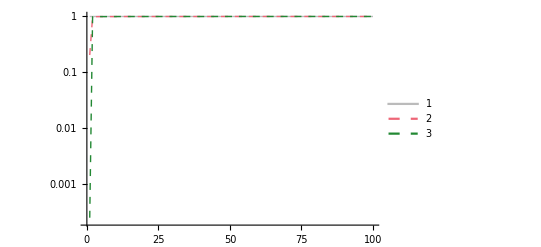
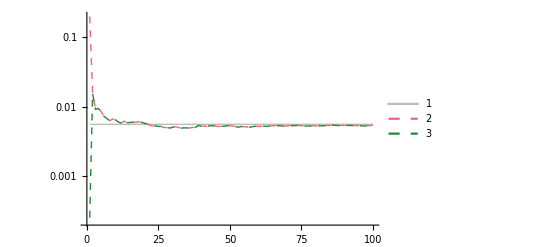
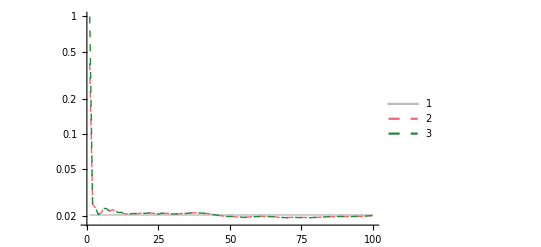
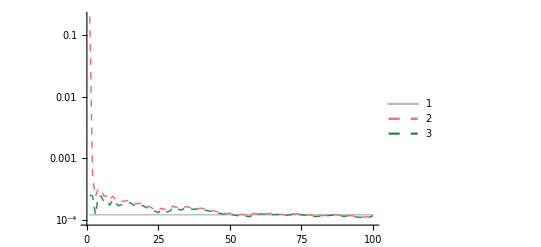
(-Graphics-
-Graphics-
-Graphics-
-Graphics-)

```mathematica
Table[ListLogPlot[{finfreqs[[s+1]]*Table[1,{Length@points}],Table[prob[s,i,4,1/4],{i,points}],Table[prob[s,i,0.001,1/4],{i,points}]},PlotStyle->{{grey,Thick},Dashed,Dashed},PlotLegends->Auto,Joined->True,PlotRange->Auto],{s,0,3}]//MF
```

```mathematica
prob[1,1,4,1/4]
```

1/5

```mathematica
T@Tally@states
```

{{2,0,1,3},{8541,406553,2317,50}}

```mathematica
{}+{0}
```

{}+{0}